CreateDirectory::filex: "C:\\Users\\Petr\\Desktop\\Projects\\Programming Techniques\\shown results\\" already exists.

CreateDirectory::filex: "C:\\Users\\Petr\\Desktop\\Projects\\Programming Techniques\\shown results\\sort\\" already exists.

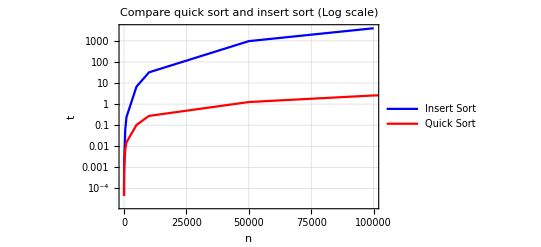

InterpolatingFunction::dmval: Input value {2.04286} lies outside the range of data in the interpolating function. Extrapolation will be used.

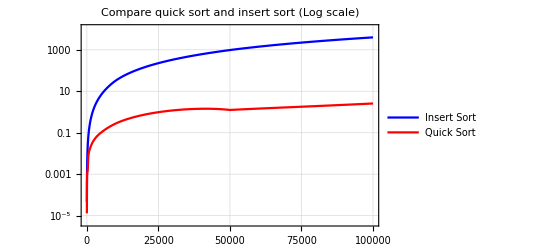

InterpolatingFunction::dmval: Input value {2.04286} lies outside the range of data in the interpolating function. Extrapolation will be used.

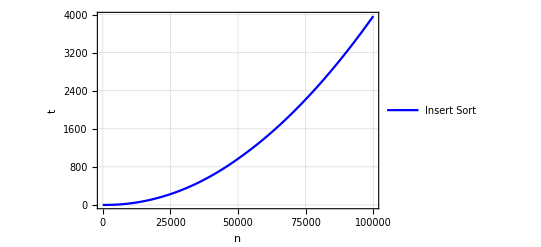

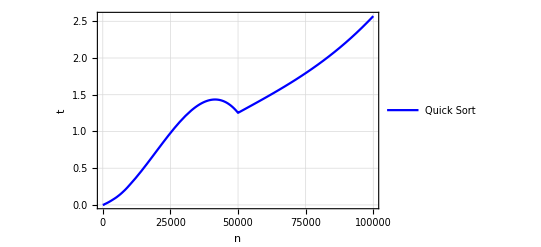

```mathematica
SetDirectory[NotebookDirectory[]];
workingDirectory = CreateDirectory["shown results"];
SetDirectory[workingDirectory];
file= OpenRead["../log_sort.txt"];
workingDirectory = CreateDirectory["sort"];
SetDirectory[workingDirectory];
filelist= ReadList[file,String];
quickSortResults = filelist[[2;;;;3]];
insertSortResults = filelist[[1;;;;3]];
insertSortResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,insertSortResults][[;;-4]];
quickSortResults= Map[({StringSplit[#][[4]],StringSplit[#][[7]]})&,quickSortResults];
insertSortResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,insertSortResults];
quickSortResults= Map[({Read[StringToStream[#[[1]]],Number],Read[StringToStream[#[[2]]],Number]})&,quickSortResults];
Plot1 = Show[ListLogPlot[insertSortResults,Joined->True,PlotStyle->Blue,PlotLegends->{"Insert Sort"},PlotLabel->"Compare quick sort and insert sort (Log scale)", AxesLabel->{"n","t"},PlotTheme->"Detailed"],ListLogPlot[quickSortResults,Joined->True,PlotStyle->Red,PlotLegends->{"Quick Sort"}]]
insertFunc = Interpolation[insertSortResults];
quickFunc = Interpolation[quickSortResults];
Plot2 = LogPlot[{insertFunc[x],quickFunc[x]},{x,0,10^5},PlotStyle->{Blue,Red},PlotLegends->{"Insert Sort","Quick Sort"},PlotLabel->"Compare quick sort and insert sort (Log scale)",PlotTheme->"Detailed"]
Plot3 = Plot[insertFunc[x],{x,0,10^5},PlotStyle->Blue,PlotLegends->{"Insert Sort"},AxesLabel->{"n","t"},PlotTheme->"Detailed"]
Plot4 = Plot[quickFunc[x],{x,0,10^5},PlotStyle->Blue,PlotLegends->{"Quick Sort"},AxesLabel->{"n","t"},PlotTheme->"Detailed"]
```

```mathematica
Export["Comp1.gif",Plot1,ImageSize->2048];
Export["Comp2.gif",Plot2,ImageSize->2048];
Export["Insert.gif",Plot3,ImageSize->2048];
Export["Quick.gif",Plot4,ImageSize->2048];
```

```mathematica
grid = Grid[Transpose[{Join[{"Time"},quickSortResults[[All,1]]],Join[{"Insert sort"},insertSortResults[[All,2]],{"-","-","-"}],Join[{"Quick sort"},quickSortResults[[All,2]]]}],Frame->All,Alignment->Left,Background->{None,{Yellow}},ItemStyle->Directive[FontSize->20,Bold]]
```

Time | Insert sort | Quick sort
5 | 0.0000443539 | 0.0000432542
10 | 0.0000593829 | 0.000120599
50 | 0.000734222 | 0.000662743
100 | 0.00263448 | 0.0010425
500 | 0.0628488 | 0.0071769
1000 | 0.245381 | 0.0155404
5000 | 6.73838 | 0.10255
10000 | 32.0763 | 0.275416
50000 | 970.909 | 1.25378
100000 | 3967.55 | 2.56999
500000 | - | 16.4959
1000000 | - | 53.5777
5000000 | - | 245.892

```mathematica
Export["TableSort.gif",grid,ImageSize->{2048,720}];
Export["TableSort.xls",grid,ImageSize->{2048,720}];
```